```mathematica
data=With[
{
Σ1=1,μ01=0.75,
Σ2=0.5,μ02=0.5
},
{
a->5,
Subscript[Σ, a,1]->0.55,Subscript[Σ, tr,1]->Σ1-μ01 (Σ1-0.55),
Subscript[Σ, a,2]->0.10,Subscript[Σ, tr,2]->Σ2-μ02 (Σ2-0.10)
}
];
```

```mathematica
Subscript[J, Q][x_]:=SubPlus[Q][x]-SubMinus[Q][x]
```

```mathematica
Σ[x_]:=Piecewise[{{Subscript[Σ, tr,1], Abs[x]≤a}, {Subscript[Σ, tr,2], Abs[x]>a}}]
```

```mathematica
fp[x_,ϕ_]:= 1/2(ϕ[x]-1/Σ[x] ϕ'[x]+1/Σ[x] Subscript[J, S][x]);
fm[x_,ϕ_]:= 1/2(ϕ[x]+1/Σ[x] ϕ'[x]-1/Σ[x] Subscript[J, S][x]);
```

```mathematica
plt:=Plot[Evaluate[{ϕ[x],fp[x,ϕ],fm[x,ϕ]}/.data],Evaluate[{x,-a-4,a+4}/.data],(*AxesLabel->{"x [cm]","tok [cm^-1s^-1]"}*)AxesStyle->Directive[Thick,14],PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Green]},
Epilog->{
{Dashed,Line[Evaluate[{{a,0},{a,1.25ϕ[0]}}/.data]]},{Dashed,Line[Evaluate[{{-a,0},{-a,1.25ϕ[0]}}/.data]]}
},
ImageSize->Scaled[0.8]
];
```

```mathematica
SubPlus[Q][x_]:=Piecewise[{{1/(2a), Abs[x]<a}, {0, Abs[x]≥a}}];
SubMinus[Q][x_]:=Piecewise[{{1/(2a), Abs[x]<a}, {0, Abs[x]≥a}}];
```

```mathematica
A=-1/(2a Subscript[Σ, a,1])1/(Cosh[√(Subscript[Σ, a,1] Subscript[Σ, tr,1])a]+√(Subscript[Σ, a,1]/Subscript[Σ, a,2] Subscript[Σ, tr,2]/Subscript[Σ, tr,1])Sinh[√(Subscript[Σ, a,1] Subscript[Σ, tr,1])a]);
B=1/(2a Subscript[Σ, a,1])√(Subscript[Σ, a,1]/Subscript[Σ, a,2] Subscript[Σ, tr,2]/Subscript[Σ, tr,1])(Sinh[√(Subscript[Σ, a,1] Subscript[Σ, tr,1])a]Exp[√(Subscript[Σ, a,2] Subscript[Σ, tr,2])a])/(Cosh[√(Subscript[Σ, a,1] Subscript[Σ, tr,1])a]+√(Subscript[Σ, a,1]/Subscript[Σ, a,2] Subscript[Σ, tr,2]/Subscript[Σ, tr,1])Sinh[√(Subscript[Σ, a,1] Subscript[Σ, tr,1])a]);
```

```mathematica
ϕ[x_]:=Piecewise[{{1/(2a Subscript[Σ, a,1])+A Cosh[√(Subscript[Σ, a,1] Subscript[Σ, tr,1])x], Abs[x]≤a}, {B Exp[-√(Subscript[Σ, a,2] Subscript[Σ, tr,2])x], x>a}, {B Exp[√(Subscript[Σ, a,2] Subscript[Σ, tr,2])x], x<-a}}];
```

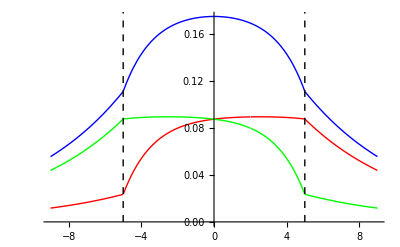

```mathematica
plt
```

```mathematica
SubPlus[S]=0.7;SubMinus[S]=0.3;xS=2;
SubPlus[Q][x_]=Piecewise[{{SubPlus[S], x==xS}, {0, x≠xS}}];
SubMinus[Q][x_]=Piecewise[{{SubMinus[S], x==xS}, {0, x≠xS}}];
```

```mathematica
A=1/(2(1-((√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])-1)/(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])+1))^2 Exp[-2 √(Subscript[Σ, a,1] Subscript[Σ, tr,1])a]))(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])(SubPlus[S]+SubMinus[S])(1-(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])-1)/(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])+1)Exp[-2 √(Subscript[Σ, a,1] Subscript[Σ, tr,1])(a-xS)])-(SuperPlus[Q]-SuperMinus[Q])(1+(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])-1)/(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])+1)Exp[-2 √(Subscript[Σ, a,1] Subscript[Σ, tr,1])(a-xS)]));
B=-A(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])-1)/(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])+1)Exp[-2 √(Subscript[Σ, a,1] Subscript[Σ, tr,1])xS];
G=1/(2(1-((√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])-1)/(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])+1))^2 Exp[-2 √(Subscript[Σ, a,1] Subscript[Σ, tr,1])a]))(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])(SubPlus[S]+SubMinus[S])(1-(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])-1)/(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])+1)Exp[-2 √(Subscript[Σ, a,1] Subscript[Σ, tr,1])xS])+(SuperPlus[Q]-SuperMinus[Q])(1+(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])-1)/(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])+1)Exp[-2 √(Subscript[Σ, a,1] Subscript[Σ, tr,1])xS]));
H=-G(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])-1)/(√(Subscript[Σ, tr,1]/Subscript[Σ, a,1])+1)Exp[-2 √(Subscript[Σ, a,1] Subscript[Σ, tr,1])(a-xS)];
```

```mathematica
ϕ[x_]:=Piecewise[{{A Exp[-√(Subscript[Σ, a,1] Subscript[Σ, tr,1])(xS-x)]+B Exp[√(Subscript[Σ, a,1] Subscript[Σ, tr,1])(xS-x)], x<xS}, {G Exp[-√(Subscript[Σ, a,1] Subscript[Σ, tr,1])(x-xS)]+H Exp[√(Subscript[Σ, a,1] Subscript[Σ, tr,1])(x-xS)], x>xS}}];
```

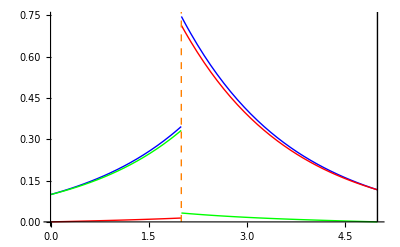

```mathematica
Plot[Evaluate[{ϕ[x],fp[x,ϕ],fm[x,ϕ]}/.data],Evaluate[{x,0,a}/.data],(*AxesLabel->{"x [cm]","tok [cm^-1s^-1]"}*)AxesStyle->Directive[Thick,14],PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Green]},
Epilog->{
{Line[Evaluate[{{a,0},{a,1.25ϕ[xS+0.001]}}/.data]]},
{Dashed,Orange,Line[Evaluate[{{xS,0},{xS,1.25ϕ[xS+0.001]}}/.data]]}
},
ImageSize->Scaled[0.8]
]
```